## Initialization

```mathematica
SetDirectory[NotebookDirectory[]];
SetOptions[Plot,Frame->True,ImageSize->Scaled[.7],FrameTicks->All,LabelStyle->Directive[FontSize->14,Black,FontOpacity->0.999,FontFamily->"Helvetica"],FrameTicksStyle->Directive[FontSize->12,Black,Plain],PlotPoints->200,PlotRange->All];
SetOptions[LogLinearPlot,Frame->True,ImageSize->Scaled[.7],FrameTicks->All,LabelStyle->Directive[FontSize->14,Black,FontOpacity->0.999,FontFamily->"Helvetica"],FrameTicksStyle->Directive[FontSize->12,Black,Plain],PlotPoints->200,PlotRange->All];
SetOptions[ListLogLinearPlot,Frame->True,ImageSize->Scaled[.7],FrameTicks->All,LabelStyle->Directive[FontSize->14,Black,FontOpacity->0.999,FontFamily->"Helvetica"],FrameTicksStyle->Directive[FontSize->12,Black,Plain],PlotRange->All];
SetOptions[ListLogLogPlot,Frame->True,ImageSize->Scaled[.7],FrameTicks->All,LabelStyle->Directive[FontSize->14,Black,FontOpacity->0.999,FontFamily->"Helvetica"],FrameTicksStyle->Directive[FontSize->12,Black,Plain],PlotRange->All];
```

## Testing

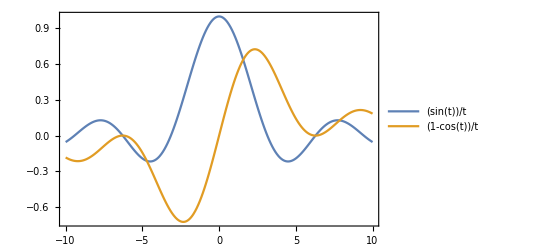

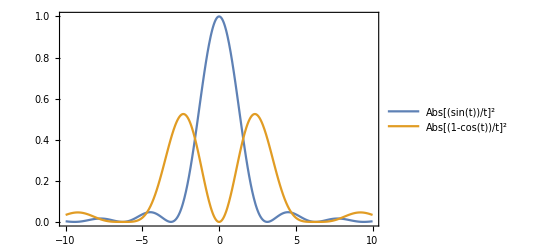

```mathematica
Plot[{Sin[t]/t,(1-Cos[t])/t},{t,-10,10},PlotLegends->"Expressions"]
Plot[{Abs[Sin[t]/t]^2,Abs[(1-Cos[t])/t]^2},{t,-10,10},PlotLegends->"Expressions"]
```